Valid MC samples = 1000

Rc = 1.1046 +/- 0.0434674

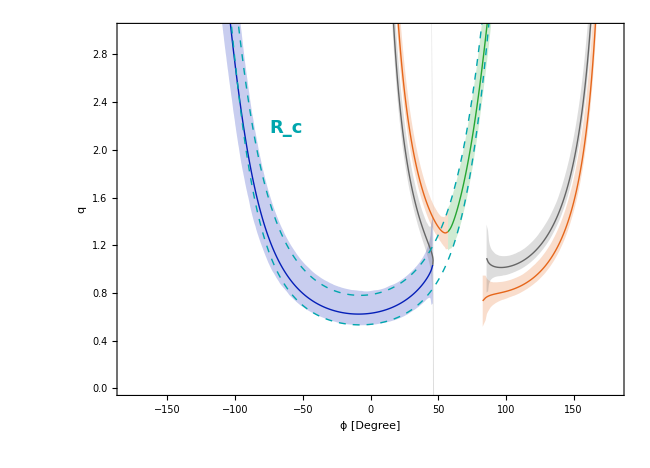

```mathematica
ClearAll["Global`*"];

SetDirectory[NotebookDirectory[]];

Get["inputs.wl"];
Get["parameters.wl"];

(* ==============================================*)
(*Basic helpers*)
(* ==============================================*)

ClearAll[validPointQ,pc,ampMag,triangleAngle,splitCurve,tangent2D,normal2D,drawPositive,drawAny,buildBranchData,samplePars,branchPiecesFromIndices,makeBandPolygon,qRcCurves];

validPointQ[pt_]:=MatchQ[pt,{_?NumericQ,_?NumericQ}];

pc[mB_,m1_,m2_]:=Sqrt[(mB^2-(m1+m2)^2) (mB^2-(m1-m2)^2)]/(2 mB);

ampMag[br_,tau_,mB_,m1_,m2_]:=Sqrt[N[br/(tau*pc[mB,m1,m2]),20]];

triangleAngle[a_,b_,x_,sign_:1]:=Module[{cosa},cosa=N[(x^2+a^2-b^2)/(2 x a),20];
cosa=Chop[Re[cosa]];
If[NumericQ[cosa]&&-1<=cosa<=1,sign ArcCos[cosa],Indeterminate]];

splitCurve[data_List,jump_:35]:=Module[{clean,pieces={},current,dphi},clean=Cases[data,{_?NumericQ,_?NumericQ}];
If[clean==={},Return[{}]];
current={First[clean]};
Do[dphi=Abs[clean[[i,1]]-clean[[i-1,1]]];
If[dphi>jump,AppendTo[pieces,current];
current={clean[[i]]},AppendTo[current,clean[[i]]]],{i,2,Length[clean]}];
AppendTo[pieces,current];
pieces];

tangent2D[data_,k_]:=Module[{n=Length[data],v},If[n<2,Return[{1.,0.}]];
Which[k<=1,v=data[[Min[2,n]]]-data[[1]],k>=n,v=data[[n]]-data[[Max[1,n-1]]],True,v=data[[k+1]]-data[[k-1]]];
v=Chop@Re@N[v,20];
If[!VectorQ[v,NumericQ]||Length[v]!=2||Norm[v]==0,{1.,0.},v/Norm[v]]];

normal2D[data_,k_]:=Module[{t},t=tangent2D[data,k];
Chop@Re@N[{-t[[2]],t[[1]]},20]];

drawPositive[mu_,sigma_]:=Module[{x=RandomVariate[NormalDistribution[mu,sigma]]},While[x<=0,x=RandomVariate[NormalDistribution[mu,sigma]]];
x];

drawAny[mu_,sigma_]:=RandomVariate[NormalDistribution[mu,sigma]];

(* ==============================================*)
(*Central values and errors*)
(* ==============================================*)

centralPars=<|"gamma"->gamma0,"RTC"->RTC0,"Vus"->Vus0,"Vud"->Vud0,"rhoc"->rhoc0,"thetac"->thetac0,"rc"->rc0,"deltac"->deltac0,"AcpPiPlusK0"->AcppipKs0,"AcpPi0KPlus"->Acppi0Kp0,"BrPiPlusK0"->BrBppipK00,"BrPi0KPlus"->BrBppi0Kp0,"BrPiPlusPi0"->BrBppippi00|>;

errorPars=<|"gamma"->gammaErr,"RTC"->RTCErr,"Vus"->VusErr,"Vud"->VudErr,"rhoc"->rhocErr,"thetac"->thetacErr,"rc"->rcErr,"deltac"->deltacErr,"AcpPiPlusK0"->AcppipKsErr,"AcpPi0KPlus"->Acppi0KpErr,"BrPiPlusK0"->BrBppipK0Err,"BrPi0KPlus"->BrBppi0KpErr,"BrPiPlusPi0"->BrBppippi0Err|>;

(* ==============================================*)
(*Build all 8 central lines*)
(* ==============================================*)

buildBranchData[pars_Association,nGrid_:350]:=Module[{gammaVal,RTCVal,epsVal,AcpPiPlusK0,AcpPi0KPlus,BrPiPlusK0,BrPi0KPlus,BrPiPlusPi0,Aplus0Mag,Abarplus0Mag,A0plusMag,Abar0plusMag,ApiPiMag,TpCpMag,Aplus0Model,Abarplus0Model,phiCVal,xMin1,xMax1,xMin2,xMax2,xMin,xMax,tGrid,xGrid,signPairs,qPhiPointLocal,deltaPhi32Local,branchData},gammaVal=pars["gamma"];
RTCVal=pars["RTC"];
epsVal=pars["Vus"]/pars["Vud"];
AcpPiPlusK0=pars["AcpPiPlusK0"];
AcpPi0KPlus=pars["AcpPi0KPlus"];
BrPiPlusK0=pars["BrPiPlusK0"];
BrPi0KPlus=pars["BrPi0KPlus"];
BrPiPlusPi0=pars["BrPiPlusPi0"];
Aplus0Mag=ampMag[BrPiPlusK0 (1-AcpPiPlusK0),TBp0,MBp0,Mpip0,MK00];
Abarplus0Mag=ampMag[BrPiPlusK0 (1+AcpPiPlusK0),TBp0,MBp0,Mpip0,MK00];
A0plusMag=Sqrt[2] ampMag[BrPi0KPlus (1-AcpPi0KPlus),TBp0,MBp0,Mpi00,MKp0];
Abar0plusMag=Sqrt[2] ampMag[BrPi0KPlus (1+AcpPi0KPlus),TBp0,MBp0,Mpi00,MKp0];
ApiPiMag=Sqrt[2] ampMag[BrPiPlusPi0,TBp0,MBp0,Mpip0,Mpi00];
TpCpMag=RTCVal*epsVal*ApiPiMag;
TpCpMag=Chop@Re@N[TpCpMag,20];
If[!NumericQ[TpCpMag]||TpCpMag<=0,Return[$Failed]];
Aplus0Model=1+pars["rhoc"] Exp[I pars["thetac"]] Exp[I gammaVal];
Abarplus0Model=1+pars["rhoc"] Exp[I pars["thetac"]] Exp[-I gammaVal];
phiCVal=Arg[Abarplus0Model Conjugate[Aplus0Model]];
phiCVal=Chop@Re@N[phiCVal,20];
xMin1=Abs[Aplus0Mag-A0plusMag];
xMax1=Aplus0Mag+A0plusMag;
xMin2=Abs[Abarplus0Mag-Abar0plusMag];
xMax2=Abarplus0Mag+Abar0plusMag;
xMin=Max[xMin1,xMin2];
xMax=Min[xMax1,xMax2];
xMin=Chop@Re@N[xMin,20];
xMax=Chop@Re@N[xMax,20];
If[!(NumericQ[xMin]&&NumericQ[xMax]&&xMin<xMax),Return[$Failed]];
tGrid=Subdivide[0.,1.,nGrid];
xGrid=xMin+tGrid (xMax-xMin);
signPairs=Tuples[{-1,1},2];
deltaPhi32Local[x_,{s1_,s2_}]:=Module[{alpha,beta,val},alpha=triangleAngle[Aplus0Mag,A0plusMag,x,s1];
beta=phiCVal+triangleAngle[Abarplus0Mag,Abar0plusMag,x,s2];
val=If[NumericQ[alpha]&&NumericQ[beta],alpha-beta,Indeterminate];
If[NumericQ[val],Chop@Re@N[val,20],Indeterminate]];
qPhiPointLocal[x_,dphi_,eta_]:=Module[{Nval,cval,sval,qval,phival,pt},Nval=x/TpCpMag;
cval=eta Nval Cos[dphi/2];
sval=eta Nval Sin[dphi/2];
qval=Sqrt[(Cos[gammaVal]-cval)^2+(Sin[gammaVal]-sval)^2];
phival=Arg[(Cos[gammaVal]-cval)+I (Sin[gammaVal]-sval)];
pt=Chop@Re@N[{phival/Degree,qval},20];
If[validPointQ[pt],pt,Missing["InvalidPoint"]]];
branchData=Table[Module[{dphiList,curvePlus,curveMinus},dphiList=Table[deltaPhi32Local[xGrid[[k]],signPairs[[i]]],{k,Length[xGrid]}];
curvePlus=Table[If[NumericQ[dphiList[[k]]],qPhiPointLocal[xGrid[[k]],dphiList[[k]],1],Missing["InvalidPoint"]],{k,Length[xGrid]}];
curveMinus=Table[If[NumericQ[dphiList[[k]]],qPhiPointLocal[xGrid[[k]],dphiList[[k]],-1],Missing["InvalidPoint"]],{k,Length[xGrid]}];
{curvePlus,curveMinus}],{i,Length[signPairs]}];
<|"BranchData"->branchData,"TGrid"->tGrid|>];

(* ==============================================*)
(*Generate Monte Carlo sampled inputs*)
(* ==============================================*)

samplePars[]:=<|"gamma"->drawAny[centralPars["gamma"],errorPars["gamma"]],"RTC"->drawPositive[centralPars["RTC"],errorPars["RTC"]],"Vus"->drawPositive[centralPars["Vus"],errorPars["Vus"]],"Vud"->drawPositive[centralPars["Vud"],errorPars["Vud"]],"rhoc"->drawPositive[centralPars["rhoc"],errorPars["rhoc"]],"thetac"->drawAny[centralPars["thetac"],errorPars["thetac"]],"rc"->drawPositive[centralPars["rc"],errorPars["rc"]],"deltac"->drawAny[centralPars["deltac"],errorPars["deltac"]],"AcpPiPlusK0"->drawAny[centralPars["AcpPiPlusK0"],errorPars["AcpPiPlusK0"]],"AcpPi0KPlus"->drawAny[centralPars["AcpPi0KPlus"],errorPars["AcpPi0KPlus"]],"BrPiPlusK0"->drawPositive[centralPars["BrPiPlusK0"],errorPars["BrPiPlusK0"]],"BrPi0KPlus"->drawPositive[centralPars["BrPi0KPlus"],errorPars["BrPi0KPlus"]],"BrPiPlusPi0"->drawPositive[centralPars["BrPiPlusPi0"],errorPars["BrPiPlusPi0"]]|>;

(* ==============================================*)
(*Central branch data and samples*)
(* ==============================================*)

nGrid=1350;
nSamples=1000;

centralResult=buildBranchData[centralPars,nGrid];
If[centralResult===$Failed,Print["Central branch construction failed."];
Abort[];];

branchData=centralResult["BranchData"];

sampleResults=DeleteCases[Table[Module[{res},res=buildBranchData[samplePars[],nGrid];
If[res===$Failed,Nothing,res["BranchData"]]],{nSamples}],Nothing];

Print["Valid MC samples = ",Length[sampleResults]];

(* ==============================================*)
(*Color setting*)
(*only blue changed darker*)
(* ==============================================*)

branchColors={RGBColor[0.90,0.40,0.10],(*orange*)RGBColor[0.15,0.65,0.20],(*green*)RGBColor[0.02,0.12,0.72],(*darker blue*)GrayLevel[0.40]               (*gray*)};

(* ==============================================*)
(*Split branch by valid-index pieces*)
(* ==============================================*)

branchPiecesFromIndices[curve_,jump_:40]:=Module[{validIdx,pieces={},current={},dphi},validIdx=Flatten@Position[curve,{_?NumericQ,_?NumericQ}];
If[validIdx==={},Return[{}]];
current={First[validIdx]};
Do[dphi=Abs[curve[[validIdx[[i]],1]]-curve[[validIdx[[i-1]],1]]];
If[dphi>jump,AppendTo[pieces,current];
current={validIdx[[i]]},AppendTo[current,validIdx[[i]]]],{i,2,Length[validIdx]}];
AppendTo[pieces,current];
pieces];

(* ==============================================*)
(*Construct one polygon for one piece*)
(* ==============================================*)

makeBandPolygon[centralCurve_,sampleCurves_,idxPiece_List]:=Module[{upperPts={},lowerPts={},pos,k,center,subcurve,nn,pts,proj,qlo,qhi},subcurve=centralCurve[[idxPiece]];
subcurve=Cases[subcurve,{_?NumericQ,_?NumericQ}];
subcurve=Chop@Re@N[subcurve,20];
If[Length[subcurve]<3,Return[Nothing]];
Do[k=idxPiece[[pos]];
center=centralCurve[[k]];
If[!validPointQ[center],Continue[]];
center=Chop@Re@N[center,20];
nn=normal2D[subcurve,pos];
If[!VectorQ[nn,NumericQ]||Length[nn]!=2,Continue[]];
pts=Cases[sampleCurves[[All,k]],{_?NumericQ,_?NumericQ}];
pts=Chop@Re@N[pts,20];
pts=Select[pts,validPointQ];
If[Length[pts]<10,Continue[]];
proj=((#-center).nn)&/@pts;
proj=Chop@Re@N[proj,20];
proj=Select[proj,NumericQ];
If[Length[proj]<10,Continue[]];
qlo=Quantile[proj,0.16];
qhi=Quantile[proj,0.84];
AppendTo[upperPts,center+qhi nn];
AppendTo[lowerPts,center+qlo nn];,{pos,Length[idxPiece]}];
upperPts=Select[upperPts,validPointQ];
lowerPts=Select[lowerPts,validPointQ];
If[Length[upperPts]<3||Length[lowerPts]<3,Nothing,Polygon@Join[upperPts,Reverse[lowerPts]]]];

(* ==============================================*)
(*Plot all 8 branches:original functionality*)
(* ==============================================*)

bandGraphicsAll=Graphics[Flatten@Table[Module[{centralCurve,sampleCurves,pieces,polys},centralCurve=branchData[[i,s]];
sampleCurves=sampleResults[[All,i,s]];
pieces=branchPiecesFromIndices[centralCurve,40];
polys=DeleteCases[makeBandPolygon[centralCurve,sampleCurves,#]&/@pieces,Nothing];
If[polys==={},{},{Directive[branchColors[[i]],Opacity[0.20],EdgeForm[None]],polys}]],{i,1,4},{s,1,2}]];

branchPlotsAll=Flatten@Table[Module[{pieces1},pieces1=splitCurve[branchData[[i,s]],40];
If[pieces1==={},Nothing,ListLinePlot[pieces1,PlotStyle->Directive[branchColors[[i]],Thick],InterpolationOrder->1]]],{i,1,4},{s,1,2}];

branchPlotsAll=DeleteCases[branchPlotsAll,Nothing];

branchPlotAll=Show[bandGraphicsAll,Sequence@@branchPlotsAll,Frame->True,Axes->False,FrameStyle->Directive[Black,14],FrameTicksStyle->Directive[Black,12],FrameLabel->{Style["ϕ [Degree]",16,Black],Style["q",16,Black]},PlotRange->{{-180,180},{0,2}},PlotRangePadding->Scaled[0.02],ImageSize->650,AspectRatio->0.72,Background->White];

(* ==============================================*)
(*Rc constraint*)
(*Rc=2 Br(B+ ->pi0 K+)/Br(B+ ->pi+K0)*)
(*IMPORTANT:use BrBppi0Kp0 and BrBppipK00*)
(* ==============================================*)

Rc0=2 BrBppi0Kp0/BrBppipK00;

RcErr=Rc0 Sqrt[(BrBppi0KpErr/BrBppi0Kp0)^2+(BrBppipK0Err/BrBppipK00)^2];

Print["Rc = ",N[Rc0,6]," +/- ",N[RcErr,6]];

qRcCurves[phiDegGrid_,RcVal_,gammaVal_,rhocVal_,thetacVal_,rcVal_,deltacVal_]:=Module[{phi,A,B,C,disc,qPlus,qMinus},Table[phi=phiDeg Degree;
A=rcVal^2;
B=2 rcVal (Cos[deltacVal] Cos[phi]-(rcVal-rhocVal Cos[thetacVal-deltacVal]) Cos[gammaVal-phi]);
C=(1+2 rhocVal Cos[thetacVal] Cos[gammaVal]+rhocVal^2) (1-RcVal)-2 rhocVal rcVal Cos[thetacVal-deltacVal]-2 rcVal Cos[deltacVal] Cos[gammaVal]+rcVal^2;
disc=Chop@Re@N[B^2-4 A C,20];
If[NumericQ[disc]&&disc>=0,qPlus=Chop@Re@N[(-B+Sqrt[disc])/(2 A),20];
qMinus=Chop@Re@N[(-B-Sqrt[disc])/(2 A),20];
{If[NumericQ[qPlus]&&qPlus>0,{phiDeg,qPlus},Missing["Invalid"]],If[NumericQ[qMinus]&&qMinus>0,{phiDeg,qMinus},Missing["Invalid"]]},{Missing["Invalid"],Missing["Invalid"]}],{phiDeg,phiDegGrid}]];

phiGridRc=Subdivide[-180,180,1600];

rcCentralData=qRcCurves[phiGridRc,Rc0,gamma0,rhoc0,thetac0,rc0,deltac0];
rcLowData=qRcCurves[phiGridRc,Rc0-RcErr,gamma0,rhoc0,thetac0,rc0,deltac0];
rcHighData=qRcCurves[phiGridRc,Rc0+RcErr,gamma0,rhoc0,thetac0,rc0,deltac0];

rcCentralPlus=Cases[rcCentralData[[All,1]],{_?NumericQ,_?NumericQ}];
rcCentralMinus=Cases[rcCentralData[[All,2]],{_?NumericQ,_?NumericQ}];

rcLowPlus=Cases[rcLowData[[All,1]],{_?NumericQ,_?NumericQ}];
rcLowMinus=Cases[rcLowData[[All,2]],{_?NumericQ,_?NumericQ}];

rcHighPlus=Cases[rcHighData[[All,1]],{_?NumericQ,_?NumericQ}];
rcHighMinus=Cases[rcHighData[[All,2]],{_?NumericQ,_?NumericQ}];

rcColor=RGBColor[0.0,0.65,0.68];

(*no Rc shading and no Rc central curve*)
rcPlots=DeleteCases[{If[rcLowPlus==={},Nothing,ListLinePlot[splitCurve[rcLowPlus,8],PlotStyle->Directive[rcColor,Dashed,Thick],InterpolationOrder->1]],If[rcLowMinus==={},Nothing,ListLinePlot[splitCurve[rcLowMinus,8],PlotStyle->Directive[rcColor,Dashed,Thick],InterpolationOrder->1]],If[rcHighPlus==={},Nothing,ListLinePlot[splitCurve[rcHighPlus,8],PlotStyle->Directive[rcColor,Dashed,Thick],InterpolationOrder->1]],If[rcHighMinus==={},Nothing,ListLinePlot[splitCurve[rcHighMinus,8],PlotStyle->Directive[rcColor,Dashed,Thick],InterpolationOrder->1]]},Nothing];

rcLabelGraphic=Graphics[Text[Style[Subscript["R","c"],18,rcColor,Bold],{-62,2.18}]];

(* ==============================================*)
(*Keep selected charged branches*)
(*6 branches in total:orange:both green:one blue:one gray:both*)
(* ==============================================*)

keepBranches={{1,1},{1,2},{2,1},{3,1},{4,1},{4,2}};

bandGraphicsSelected=Graphics[Flatten@Table[Module[{i,s,centralCurve,sampleCurves,pieces,polys},i=br[[1]];
s=br[[2]];
centralCurve=branchData[[i,s]];
sampleCurves=sampleResults[[All,i,s]];
pieces=branchPiecesFromIndices[centralCurve,40];
polys=DeleteCases[makeBandPolygon[centralCurve,sampleCurves,#]&/@pieces,Nothing];
If[polys==={},{},{Directive[branchColors[[i]],Opacity[0.22],EdgeForm[None]],polys}]],{br,keepBranches}]];

branchPlotsSelected=DeleteCases[Table[Module[{i,s,pieces},i=br[[1]];
s=br[[2]];
pieces=splitCurve[branchData[[i,s]],40];
If[pieces==={},Nothing,ListLinePlot[pieces,PlotStyle->Directive[branchColors[[i]],Thick],InterpolationOrder->1]]],{br,keepBranches}],Nothing];

(* ==============================================*)
(*Final plot with 6 charged branches+Rc lines*)
(*No Rc shading,no Rc central value*)
(* ==============================================*)

branchPlotWithRc=Show[bandGraphicsSelected,Sequence@@branchPlotsSelected,Sequence@@rcPlots,rcLabelGraphic,Frame->True,Axes->False,FrameStyle->Directive[Black,14],FrameTicksStyle->Directive[Black,12],FrameLabel->{Style["ϕ [Degree]",16,Black],Style["q",16,Black]},PlotRange->{{-180,180},{0,3}},PlotRangePadding->Scaled[0.02],ImageSize->650,AspectRatio->0.72,Background->White];

branchPlotWithRc
```